# 计算物理学-桂龙成

## 1. 基本运算

#### 加减乘除

```mathematica
2+3*4 - 6/7
2+3 4 -6/7
```

92/7

92/7

#### 括号(注意输入法！)

```mathematica
(2+3)*4-6/7
```

134/7

#### 高级运算

```mathematica
E^2
(3+5I)*(4-6I)
√2
Sqrt[2]//N
N[Sqrt[2]]
```

ⅇ^2

42+2 ⅈ

√2

1.41421

1.41421

#### 变量定义

```mathematica
a=3
b= √((1+x^2)/(2x+3))
?a
?b
Clear[a]
?a
Remove[b]
?b
```

3

√((x^2+1)/(2 x+3))

Global`a

a=3

Global`b

b=√((1+x^2)/(3+2 x))

Global`a

Information::notfound: 无法找到符号 b.

#### 常见函数

```mathematica
Sqrt[3.5]
8^(1/3)
Power[8,1/3]
Abs[5+12I]
Sign[-3.4]
Factorial[3.5]
RandomReal[{0,1},{2,10}]
Quotient[17,3]
Mod[17,3]
Log[10]
Log[2,10]
```

1.87083

2

2

13

-1

11.6317

(0.110361 | 0.691356 | 0.0317024 | 0.899614 | 0.482894 | 0.158073 | 0.476205 | 0.53471 | 0.955612 | 0.922048
0.583779 | 0.436757 | 0.598397 | 0.690709 | 0.391808 | 0.996873 | 0.973519 | 0.66626 | 0.566655 | 0.416773)

5

2

log(10)

(log(10))/(log(2))

```mathematica
Sin[30 Degree]
Sin[π/6]
Cos[ArcSin[x^2/(x^2 +1)]]
Print["Hello, World!"]
StringJoin["abc","def"]
StringReplace["abcdefg","bc"->"cb"]
```

1/2

1/2

√(1-x^4/((x^2+1)^2))

Hello, World!

abcdef

acbdefg

#### 赋值、替换与逻辑关系

```mathematica
f[0]=1;
f[n]:=n f[n-1];
g[x_]:=x^2/;x≥0
g[x_]:=-x^2/;x<0
f[x_]:=∫_0^x t ⅇ^t Sin[t]ⅆt
x^2+5x+6/.x->3
x+y/.{x->3,y->3}
a+a==2a
LogicalExpand[(p&&(q||r))]==LogicalExpand[(p&&q||p&&r)]
Clear[{f,g}]
```

30

6

True

True

#### 和与积，循环

```mathematica
Sum[1/n^2,{n,1,Infinity}]
Block[{n=10,k=4},Product[(n-i)/(k-i),{i,0,k-1}]]
Product[Sum[1/j,{j,1,i}],{i,2,10}]//N
Block[{mysum=0,k},Do[mysum=mysum+k,{k,5,25,2}];Print[mysum];mysum=0;

k=5;While[k≤25,mysum=mysum+k;k=k+2];Print[mysum];
mysum=0;
For[k=5,k≤25,k=k+2,mysum=mysum+k];
Print[mysum]]
```

π^2/6

210

1871.44

165

165

165

#### 绘图



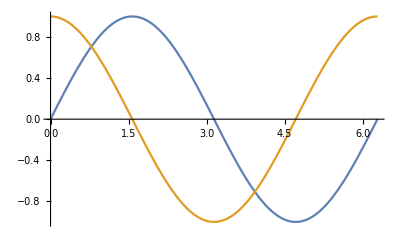

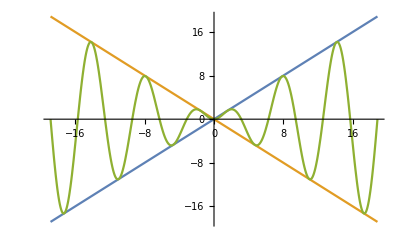

```mathematica
Plot[Sin[x],{x,0,2π}]
Plot[{Sin[x],Cos[x]},{x,0,2π}]
Plot[{x,-x,x Sin[x]},{x,-6π,6π}]
```

#### 自定义函数

{0.078125,75025}

{0.,2178309}

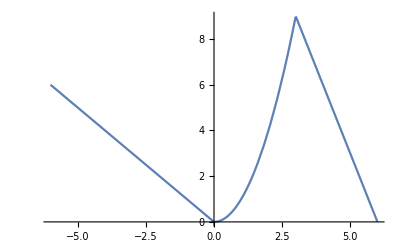

Piecewise[{{-x, x≤0}, {x^2, 0<x≤3}, {18-3 x, x>3}, {0, True}}]

Piecewise[{{-3-2 x-x^2, 3+2 x+x^2≤0}, {(3+2 x+x^2)^2, 0<3+2 x+x^2≤3}, {18-3 (3+2 x+x^2), 3+2 x+x^2>3}, {0, True}}]

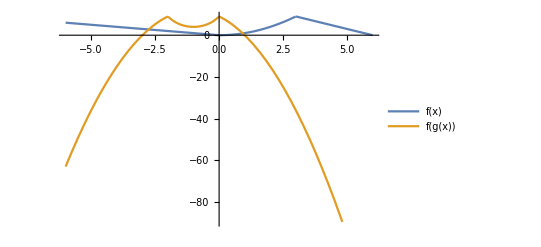

1/(1+1/(1+1/(1+1/(1+1/(1+x)))))

```mathematica
(*fibonacci 序列 定义方式一*)
Block[{f},f[1]=1;f[2]=1;f[n_]:=f[n-2]+f[n-1];Print[f[25]//Timing]]
(*fibonacci 序列 定义方式二*)
Block[{f},f[1]=1;f[2]=1;f[n_]:=f[n]=f[n-2]+f[n-1];Print[f[32]//Timing]]
(*分段函数的定义方式*)
Block[{f},f[x_]=Piecewise[{{-x,x≤ 0},{x^2,0<x≤ 3},{18-3x,x>3}}];Plot[f[x],{x,-6,6}]]
(*复合函数*)
Block[{f,g},f[x_]=Piecewise[{{-x,x≤ 0},{x^2,0<x≤ 3},{18-3x,x>3}}];g[x_]:=x^2+2x+3;

Print[f[x]];
Print[f[g[x]]];
Plot[{f[x],f[g[x]]},{x,-6,6},PlotLegends->"Expressions"]]
Block[{f},f[x_]=1/(1+x);Nest[f,x,5]]
```

#### 列表

```mathematica
(*列表运算*)
Module[{lst1,lst2},lst1={1,2,3,4,5};
lst2={2,3,2,3,2};Print["加法  ",lst1+lst2,"\n 乘法  ",lst1*lst2,"\n 乘方  ",lst1^lst2]]
```

加法  {3,5,5,7,7}
 乘法  {2,6,6,12,10}
 乘方  {1,8,9,64,25}

```mathematica
(*列表生成*)
Range[1/3,1,1/12]
Table[i+j,{i,4},{j,5}]
Array[Sin,10,{0,π}]
```

{1/3,5/12,1/2,7/12,2/3,3/4,5/6,11/12,1}

(2 | 3 | 4 | 5 | 6
3 | 4 | 5 | 6 | 7
4 | 5 | 6 | 7 | 8
5 | 6 | 7 | 8 | 9)

{0,sin(π/9),sin((2 π)/9),(√3)/2,cos(π/18),cos(π/18),(√3)/2,sin((2 π)/9),sin(π/9),0}

```mathematica
(*列表操作*)
Module[{lst},lst=Characters["Mathematics"];
Print["列表长度：",Length[lst],"\n列表首元素",First[lst],"\n列表末元素",Last[lst],"\n第四个元素",lst[[4]],"\n 排序",Sort[lst],"\n 反转",StringJoin[Reverse[lst]]]]
```

列表长度：11
列表首元素M
列表末元素s
第四个元素h
 排序{a,a,c,e,h,i,m,M,s,t,t}
 反转scitamehtaM

## 2. 解方程

#### 求解代数方程

```mathematica
Solve[7x+3==3x+8]
Solve[a x+b==c x+d,{x}]
Solve[{2 x+3y ==7,3 x + 4 y ==10},{x,y}]
√(x^2+y^2)/.Solve[{x^2 +y==5,x+y==3},{x,y}]
(*数值解*)
NSolve[x^(1/3)+√x+x==10,x]
Solve[a x+b==c x+d,x]
Reduce[a x+b==c x+d,x]
```

{{x→5/4}}

{{x→(d-b)/(a-c)}}

{{x→2,y→1}}

{√17,√5}

{{x→5.79617}}

{{x→(d-b)/(a-c)}}

(b==d∧a==c)∨(a-c≠0∧x==(d-b)/(a-c))

```mathematica
(*求解超越方程*)
Solve[Sin[x]==x^2-1,x]
FindRoot[Sin[x]==x^2-1,{x,-π,π}]
FindRoot[x+Sin[x]==0,{x,100},MaxIterations->15]
```

Solve::nsmet: 无法利用 Solve 现有的方法求解该系统.

Solve[sin(x)==x^2-1,x]

{x→-0.636733}

{x→-4.47869×10^-20}

#### 代数与三角

```mathematica
(*多项式*)
Coefficient[(1+x)^10,x,3]
CoefficientList[(1+x)^10,x]
```

120

{1,10,45,120,210,252,210,120,45,10,1}

```mathematica
(*展开、因子化、合并同类项*)
Expand[(1+x)^2+(2+x)^2]
Expand[(1+x)^2+(2+x)^2,1+x]
Factor[x^3-1]
Factor[Sin[x]+Sin[y],Trig->True]
Collect[(1+a+x)^4,x,Simplify]
Expand[(1+a+x)^4,x]
```

2 x^2+6 x+5

x^2+2 x+(x+2)^2+1

(x-1) (x^2+x+1)

2 sin(x/2+y/2) cos(x/2-y/2)

4 (a+1) x^3+6 (a+1)^2 x^2+4 (a+1)^3 x+(a+1)^4+x^4

a^4+4 a^3+(6 a^2+12 a+6) x^2+6 a^2+(4 a^3+12 a^2+12 a+4) x+(4 a+4) x^3+4 a+x^4+1

```mathematica
(*有理函数和代数函数*)
Together[x^2/(x^2-1)+x/(x^2-1)]
Apart[1/((1+x)(5+x))]
```

x/(x-1)

1/(4 (x+1))-1/(4 (x+5))

## 3. 微积分

#### 极限的计算

```mathematica
Limit[Sin[x]/x,x->0]
Limit[(1+x/n)^n,n->Infinity]
Limit[1/x,x->0,Direction->1]
Limit[1/x,x->0,Direction->-1]
```

1

ⅇ^x

-∞

∞

#### 导数的计算

```mathematica
D[x^n,x]
D[Sin[x]^10,{x,4}]
D[Sin[x y]/(x^2+y^2),x,y]
D[Sin[x y]/(x^2+y^2),x,{y,2}]
Dt[Sin[x y]/(x^2+y^2)]
D[x^2Sin[y],{{x,y}}]
Sum[(D[Exp[x],{x,k}]/.x-> 0)/k!*x^k,{k,0,5}]
Series[Exp[x],{x,0,5}]
Normal[%]
```

n x^(n-1)

280 sin^10(x)+5040 sin^6(x) cos^4(x)-4680 sin^8(x) cos^2(x)

-(x y sin(x y))/(x^2+y^2)+(8 x y sin(x y))/((x^2+y^2)^3)-(2 x^2 cos(x y))/((x^2+y^2)^2)+(cos(x y))/(x^2+y^2)-(2 y^2 cos(x y))/((x^2+y^2)^2)

-2 x (1/(x^2+y^2)-(2 y^2)/((x^2+y^2)^2)) sin(x y)-(x^2 y cos(x y))/(x^2+y^2)+(y ((8 y^2)/((x^2+y^2)^3)-2/((x^2+y^2)^2))-(4 y)/((x^2+y^2)^2)) cos(x y)-2 x (-(x^2 sin(x y))/((x^2+y^2)^2)+((24 y^2)/((x^2+y^2)^4)-4/((x^2+y^2)^3)) sin(x y)-(8 x y cos(x y))/((x^2+y^2)^3))

((y ⅆx+x ⅆy) cos(x y))/(x^2+y^2)-((2 x ⅆx+2 y ⅆy) sin(x y))/((x^2+y^2)^2)

{2 x sin(y),x^2 cos(y)}

x^5/120+x^4/24+x^3/6+x^2/2+x+1

1+x+x^2/2+x^3/6+x^4/24+x^5/120+O(x^6)

x^5/120+x^4/24+x^3/6+x^2/2+x+1

#### 积分的计算

```mathematica
Integrate[1/(x^3+1),x]
Integrate[1/(x^3+1),{x,0,1}]
Integrate[Sin[x y],{x,0,1},{y,0,x}]
NIntegrate[1/(√(x^1+y^2+z^3)),{x,0,1},{y,0,1},{z,0,1}]
```

-1/6 log(x^2-x+1)+1/3 log(x+1)+(tan^-1((2 x-1)/(√3)))/(√3)

1/18 (2 √3 π+log(64))

(ℽ-1)/2

1.0885

## 4. 微分方程

#### 常微分方程

{{y[x]→ⅇ^-x C[1]+1/2 a (-Cos[x]+Sin[x])}}

{{y[x]→-1/2 a ⅇ^-x (-1+ⅇ^x Cos[x]-ⅇ^x Sin[x])}}

{{y→Function[{x},ⅇ^-x C[1]+1/2 a (-Cos[x]+Sin[x])]}}

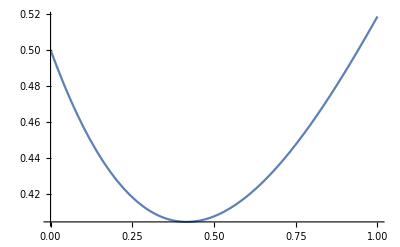

{{y[x]→InterpolatingFunction[…][x]}}

```mathematica
DSolve[y'[x]+y[x]==a Sin[x],y[x],x]
DSolve[{y'[x]+y[x]==a Sin[x],y[0]==0},y[x],x]
DSolve[y'[x]+y[x]==a Sin[x],y,x]
Plot[y[x]/.%/.{Subscript[c, 1]->1,a->1},{x,0,1}]
NDSolve[{y'[x]==x^2+√y[x],y[0]==1},y[x],{x,0,1}]
```

#### 利用拉普拉斯变换求解

```mathematica
LaplaceTransform[f''[t]+f[t]==Sin[t],t,s]
Solve[%,LaplaceTransform[f[t],t,s]]
InverseLaplaceTransform[%,s,t]
DSolve[f''[t]+f[t]==Sin[t],f,t]
```

-s f[0]+LaplaceTransform[f[t],t,s]+s^2 LaplaceTransform[f[t],t,s]-f'[0]==1/(1+s^2)

{{LaplaceTransform[f[t],t,s]→(1+s f[0]+s^3 f[0]+f'[0]+s^2 f'[0])/((1+s^2)^2)}}

{{f[t]→Cos[t] f[0]+1/2 (-t Cos[t]+Sin[t])+Sin[t] f'[0]}}

{{f→Function[{t},C[1] Cos[t]+C[2] Sin[t]+1/4 (-2 t Cos[t]-2 Cos[t]^2 Sin[t]+Cos[t] Sin[2 t])]}}

#### 波动方程

```mathematica
DSolve[(c^2 D[#,x,x]-D[#,t,t])&[y[x,t]]==0,y[x,t],{x,t}]
```

{{y(x,t)→c_1(t-x/(√(c^2)))+c_2(x/(√(c^2))+t)}}

## 5. 线性代数

#### 向量与矩阵

```mathematica
Table[i,{i,10}]
Array[Cos,10]
Table[i+j,{i,3},{j,4}]
Array[#1+#2&,{3,4}](*这里的#1+#2& 代表一个纯函数*)
DiagonalMatrix[{1,2,3}]
IdentityMatrix[3]
```

{1,2,3,4,5,6,7,8,9,10}

{cos(1),cos(2),cos(3),cos(4),cos(5),cos(6),cos(7),cos(8),cos(9),cos(10)}

(2 | 3 | 4 | 5
3 | 4 | 5 | 6
4 | 5 | 6 | 7)

(2 | 3 | 4 | 5
3 | 4 | 5 | 6
4 | 5 | 6 | 7)

(1 | 0 | 0
0 | 2 | 0
0 | 0 | 3)

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

#### 矩阵运算

```mathematica
{a,b,c} . {x,y,z}
{{a,b},{c,d}} . {x, y}
{{a,b},{c,d}} . {{r,s},{t,u}}
Cross[{a,b,c},{x,y,z}]
Inverse[({{1, 2, 3}, {4, 2, 2}, {5, 1, 7}})]
Det[({{1, 2, 3}, {4, 2, 2}, {5, 1, 7}})]
Transpose[({{1, 2, 3}, {4, 2, 2}, {5, 1, 7}})]
Tr[({{1, 2, 3}, {4, 2, 2}, {5, 1, 7}})]
MatrixPower[({{1, 2, 3}, {4, 2, 2}, {5, 1, 7}}),2]
Minors[({{1, 2, 3}, {4, 2, 2}, {5, 1, 7}}),2]
RowReduce[({{1, 2, 3}, {4, 2, 2}, {5, 1, 7}})]
Eigensystem[N[({{1, 2, 3}, {4, 2, 2}, {5, 1, 7}})]]
```

a x+b y+c z

{a x+b y,c x+d y}

(a r+b t | a s+b u
c r+d t | c s+d u)

{b z-c y,c x-a z,a y-b x}

(-2/7 | 11/42 | 1/21
3/7 | 4/21 | -5/21
1/7 | -3/14 | 1/7)

-42

(1 | 4 | 5
2 | 2 | 1
3 | 2 | 7)

10

(24 | 9 | 28
22 | 14 | 30
44 | 19 | 66)

(-6 | -10 | -2
-9 | -8 | 11
-6 | 18 | 12)

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

(9.76431 | 2.19517 | -1.95948
{-0.377661,-0.408597,-0.830915} | {-0.270002,-0.847325,0.457318} | {-0.74156,0.572381,0.349956})

## 6. 物理应用

#### 单摆

{0.0521699,{t→0.614648}}

理论最大摆角0.05217

{0.0521699,{t→0.614648}}

{0.0521699,{t→3.07324}}

T= 2.45859 s

tc= 2.45817 s

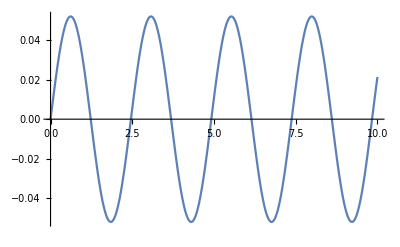

```mathematica
g=9.8;L=1.5; Ω=√(g/L);
v0=0.2;ω0=v0/L;                                               
s=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],
θ[0]==0,θ'[0]==ω0},θ,{t,0,10}];θ=θ/.s[[1]];
(*求最大摆角*)
FindMaximum[θ[t],{t,0.5}]
Print["理论最大摆角",ArcCos[1-v0^2/(2 g L)]]
θm1=FindMaximum[θ[t],{t,0.5}]
θm2=FindMaximum[θ[t],{t,3}]
T=(t/.θm2[[2]])-(t/.θm1[[2]]);
Print["T= ",T," s"]
Print["tc= ",(2π)/Ω," s"]
Plot[θ[t],{t,0,10},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
```

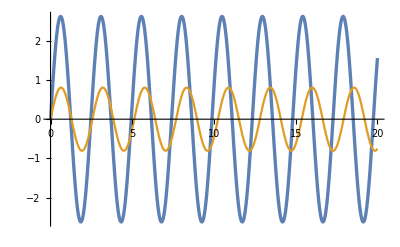

```mathematica
Clear["Global`*"]
g=9.8;L=1.5;Ω=√(g/L);
v01=1;ω01=v01/L;   v02=3;ω02=v02/L;
as=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],θ[0]==0,
θ'[0]==ω01},θ,{t,0,20}];θ1=θ/.as[[1]];
bs=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],θ[0]==0,
θ'[0]==ω02},θ,{t,0,20}];θ2=θ/.bs[[1]];
Plot[{10*θ1[t],θ2[t]},{t,0,20},PlotStyle->{Thickness[0.006],Thickness[0.004]},AxesStyle->Thickness[0.003]]
Animate[
a=ListPlot[{{θ1[t],0}},PlotRange->π/4,
PlotStyle->{Orange,PointSize[0.03]}];
b=ListPlot[{{θ2[t],0}},PlotRange->π/4,
PlotStyle->{Black,PointSize[0.03]}];
Show[{a,b}],{t,0,20},ControlPlacement->Top]
```

观察周期的计算值, 拟合计算值与角振幅的关系

```mathematica
Clear["Global`*"]
g=9.8;L=1.5;Ω=√(g/L);θT={};
Do[
ω0=v0/L;
s=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],
θ[0]==0,θ'[0]==ω0},θ,{t,0,5}];
α=θ/.s[[1]];
θm1=FindMaximum[α[t],{t,0.5}];
θm2=FindMaximum[α[t],{t,3.0}];
T=(t/.θm2[[2]])-(t/.θm1[[2]]);
AppendTo[θT,{θm1[[1]]*180/π,T}],
{v0,0.1,1.6,0.1}]
```

FindMaximum::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到函数值的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

T ≈ 2.45817-7.65618×10^-7 θ+0.0000469267 θ^2

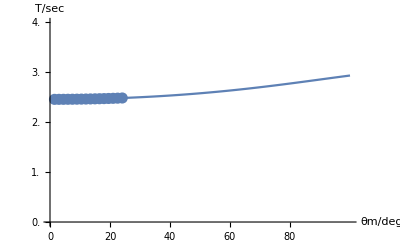

```mathematica
g1=ListPlot[θT,AxesOrigin->{0,0},
PlotStyle->PointSize[0.02]];
θT2=Fit[θT,{1,θ,θ^2,θ^3,θ^4,θ^5,θ^6},θ];
Print["T ≈ ",Take[θT2,3]]
g2=Plot[θT2,{θ,0,100},
PlotStyle->Thickness[0.004]];
Show[{g1,g2},AxesLabel->{"θm/deg","T/sec"},
PlotRange->{{0,100},{0,4}},
Ticks->{Range[0,90,10],Range[0,4,0.5]},
AxesStyle->Thickness[0.003]]
```

```mathematica
Tfit=Fit[θT,{1,θ,θ^2,θ^3,θ^4,θ^5,θ^6},θ];
len=Length[θT];
θT=Table[AppendTo[θT[[i]],Tfit/.θ->θT[[i,1]]],
{i,len}];
Partition[θT,4]//TableForm
```

1.49443
2.45828
2.45828 | 2.98912
2.45859
2.45859 | 4.48431
2.45911
2.45911 | 5.98027
2.45985
2.45985
7.47725
2.46079
2.46079 | 8.97551
2.46195
2.46195 | 10.4753
2.46332
2.46332 | 11.9769
2.4649
2.4649
13.4806
2.46671
2.46671 | 14.9866
2.46873
2.46873 | 16.4952
2.47097
2.47097 | 18.0067
2.47343
2.47343
19.5214
2.47613
2.47613 | 21.0395
2.47905
2.47905 | 22.5613
2.48221
2.48221 | 24.0872
2.4856
2.4856

#### 电力线

位于原点的正电荷的电力线分布——直接计算

y[x]/x

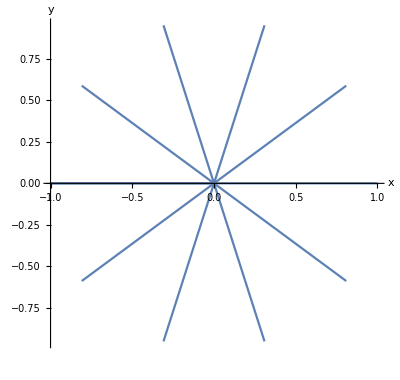

```mathematica
ϕ[x_,y_]:=1/√(x^2+y^2);
Ex=-D[ϕ[x,y],x];Ey=-D[ϕ[x,y],y];
k=(Ey/Ex)/.y->y[x]
r=10.0^-3;R=1.0;forceline={};
equ={y'[x]==k,y[xstart]==ystart};
Do[
xstart=r*Cos[θ];ystart=r*Sin[θ];
xend=R*Cos[θ];
s=NDSolve[equ,y,{x,xstart,xend}];
y=y/.s[[1]];
figure=Plot[y[x],{x,xstart,xend},
AspectRatio->Automatic,
PlotStyle->Thickness[0.004]];
AppendTo[forceline,figure];Clear[y],
{θ,-π,π,π/5.0}]
Show[forceline,PlotRange->All,
AxesStyle->Thickness[0.003],
AxesLabel->{"StyleBox[\"x\",FontSize->14]","StyleBox[\"y\",FontSize->14]"},
BaseStyle->{FontSize->12}]
Clear["Global`*"]
```

正负电荷产生的电力线——直接计算

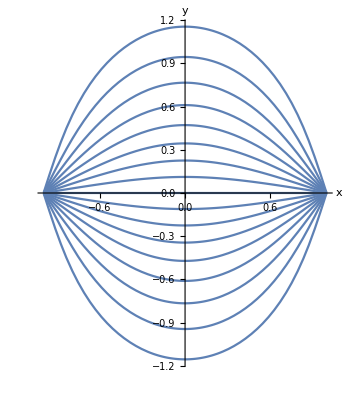

```mathematica
r=10.0^-3;a=1.0;q1=1;q2=-1;
ϕ[x_,y_]:=q1/(√((x-a)^2+y^2))+q2/(√((x+a)^2+y^2));
Ex=-D[ϕ[x,y],x];Ey=-D[ϕ[x,y],y];
k=(Ey/Ex)/.y->y[x];
θ1=π/2.0+π/10;θ2=3π/2.0-π/10;
equ={y'[x]==k,y[xstart]==ystart};
forceline={};
Do[
xstart=a+r*Cos[θ];ystart=r*Sin[θ];
xend=-(a-r);
s=NDSolve[equ,y,{x,xstart,xend}];
y=y/.s[[1]];
figure=Plot[y[x],{x,xstart,xend},
PlotStyle->Thickness[0.004],
AspectRatio->Automatic];
AppendTo[forceline,figure];
Clear[y],{θ,θ1,θ2,π/20}]
Show[forceline,PlotRange->All,
AxesStyle->Thickness[0.003],
AxesLabel->{"x","y"},
BaseStyle->{FontSize->13}]
Clear["Global`*"]
```

计算两个电荷产生的电力线——折线法

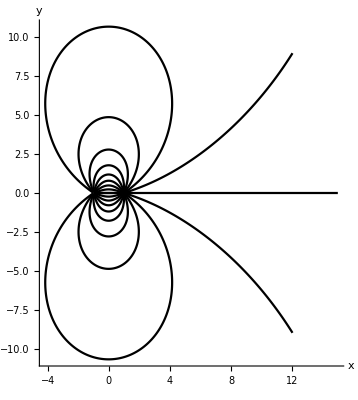

{{{1,0},{0.97,0.},{0.94,3.67394×10^-18},60,{-0.89,1.46958×10^-17},{-0.92,1.10218×10^-17},{-0.95,7.34788×10^-18}},19,{1}}
 |  |  |  |

```mathematica
p1={1,0};p2={-1,0};q1=1.0;q2=-1.0;
ψ=q1/(√((x-1)^2+y^2))+q2/(√((x+1)^2+y^2));
field=-D[ψ,x]-ⅈ*D[ψ,y];
step=0.03;r1=0.02;r2=15;forceline={};
Do[
θ=ϕ;single={p1};
Label[ss];
p=Last[single];
p=p+step*{Cos[θ],Sin[θ]};
θ=Arg[field/.{x->p[[1]],y->p[[2]]}];
If[(Norm[p1-p]>r1)∧(Norm[p2-p]>r1)∧
(Norm[p]<r2),AppendTo[single,p];Goto[ss]];
AppendTo[forceline,single],{ϕ,-π,π,π/10}]
Show[
Graphics[{Thickness[0.004],Line/@forceline}],
Axes->True,PlotRange->All,
AspectRatio->Automatic,
AxesStyle->Thickness[0.003],
AxesLabel->{"x","y"}]
Clear["Global`*"]
```

## 7. 计算物理课程中的推导

### 第三章

#### 三次样条插值

```mathematica
Clear["Global`*"]
Evaluate[Table[Symbol[x<>"i"<>p<>d],{x,{"x","y"}},{p,{"p1","","n1"}},{d,{"","d2"}}]]=Table[Subscript[Superscript[x,d],p],{x,{"x","y"}},{p,{"i+1","i","i-1"}},{d,{"","''"}}]
(*yip1d2=Subscript[Superscript["y","''"],"i+1"];
yid2=Subscript[Superscript["y","''"],"i"];
xip1=Subscript["x","i+1"];
xi=Subscript["x","i"];
yip1=Subscript["y","i+1"];
yi=Subscript["y","i"];*)
ai=(yip1d2-yid2)/(xip1-xi);
bi=(xip1*yid2-xi*yip1d2)/(xip1-xi);
ain1=(yid2-yin1d2)/(xi-xin1);
bin1=(xi*yin1d2-xin1*yid2)/(xi-xin1);
cidi=Solve[{1/6 ai*xi^3+1/2*bi*xi^2+ci*xi+di==yi,1/6 ai*xip1^3+1/2*bi*xip1^2+ci*xip1+di==yip1},{ci,di}]
cin1din1=Solve[{1/6 ain1*xin1^3+1/2*bin1*xin1^2+cin1*xin1+din1==yin1,1/6 ain1*xi^3+1/2*bin1*xi^2+cin1*xi+din1==yi},{cin1,din1}]
tmp=Simplify[1/2 ain1*xi^2+bin1*xi+cin1-1/2 ai*xi^2-bi*xi^2-ci/.cidi[[1]]/.cin1din1[[1]]]
Coefficient[tmp,yin1d2]//Simplify
Coefficient[tmp,yid2]//Simplify
Coefficient[tmp,yip1d2]//Simplify
tmp-Dot[Coefficient[tmp,{yin1d2,yid2,yip1d2}],{yin1d2,yid2,yip1d2}]//Simplify
Collect[tmp,{yin1d2,yid2,yip1d2},Simplify]
```

({(x^)_(i+1),x''_(i+1)} | {(x^)_i,x''_i} | {(x^)_(i-1),x''_(i-1)}
{(y^)_(i+1),y''_(i+1)} | {(y^)_i,y''_i} | {(y^)_(i-1),y''_(i-1)})

{{ci→-(2 (x^)_i^2 y''_(i+1)-2 (x^)_i (x^)_(i+1) y''_i+2 (x^)_i (x^)_(i+1) y''_(i+1)-2 (x^)_(i+1)^2 y''_i+(x^)_i^2 y''_i-(x^)_(i+1)^2 y''_(i+1)-6 (y^)_i+6 (y^)_(i+1))/(6 ((x^)_i-(x^)_(i+1))),di→-((x^)_i^2 (-(x^)_(i+1)) y''_i-2 (x^)_i^2 (x^)_(i+1) y''_(i+1)+2 (x^)_i (x^)_(i+1)^2 y''_i+(x^)_i (x^)_(i+1)^2 y''_(i+1)-6 (x^)_i (y^)_(i+1)+6 (y^)_i (x^)_(i+1))/(6 ((x^)_i-(x^)_(i+1)))}}

{{cin1→-(2 (x^)_i^2 y''_(i-1)-2 (x^)_i (x^)_(i-1) y''_i+2 (x^)_i (x^)_(i-1) y''_(i-1)-2 (x^)_(i-1)^2 y''_i+(x^)_i^2 y''_i-(x^)_(i-1)^2 y''_(i-1)-6 (y^)_i+6 (y^)_(i-1))/(6 ((x^)_i-(x^)_(i-1))),din1→-((x^)_i^2 (-(x^)_(i-1)) y''_i-2 (x^)_i^2 (x^)_(i-1) y''_(i-1)+2 (x^)_i (x^)_(i-1)^2 y''_i+(x^)_i (x^)_(i-1)^2 y''_(i-1)-6 (x^)_i (y^)_(i-1)+6 (y^)_i (x^)_(i-1))/(6 ((x^)_i-(x^)_(i-1)))}}

1/(6 ((x^)_i-(x^)_(i-1)) ((x^)_i-(x^)_(i+1)))((x^)_(i-1)^2 ((x^)_i-(x^)_(i+1)) (2 y''_i+y''_(i-1))+(x^)_(i-1) (2 (x^)_i (x^)_(i+1) y''_(i-1)-2 (x^)_i^2 y''_(i-1)+6 (x^)_i^3 y''_(i+1)-6 (x^)_i^2 (x^)_(i+1) y''_i-5 (x^)_i^2 y''_(i+1)+6 (x^)_i (x^)_(i+1) y''_i-2 (x^)_i (x^)_(i+1) y''_(i+1)+2 (x^)_(i+1)^2 y''_i-2 (x^)_i^2 y''_i+(x^)_(i+1)^2 y''_(i+1)+6 (y^)_i-6 (y^)_(i+1))+(x^)_(i+1) ((x^)_i^2 ((6 (x^)_i-4) y''_i-y''_(i-1)+2 y''_(i+1))-6 (y^)_i+6 (y^)_(i-1))+(x^)_i ((x^)_i^2 ((5-6 (x^)_i) y''_(i+1)+y''_(i-1))-6 (y^)_(i-1)+6 (y^)_(i+1))-(x^)_i (x^)_(i+1)^2 (2 y''_i+y''_(i+1)))

1/6 ((x^)_i-(x^)_(i-1))

(-(x^)_i ((x^)_(i-1)+2 (x^)_(i+1))+3 (x^)_i^2 (x^)_(i+1)+(x^)_(i+1) ((x^)_(i-1)-(x^)_(i+1)))/(3 ((x^)_i-(x^)_(i+1)))

(2 (x^)_i (x^)_(i+1)-6 (x^)_i^3+5 (x^)_i^2-(x^)_(i+1)^2)/(6 (x^)_i-6 (x^)_(i+1))

((x^)_(i+1) ((y^)_(i-1)-(y^)_i)+(x^)_(i-1) ((y^)_i-(y^)_(i+1))+(x^)_i ((y^)_(i+1)-(y^)_(i-1)))/(((x^)_i-(x^)_(i-1)) ((x^)_i-(x^)_(i+1)))

(y''_i (-(x^)_i ((x^)_(i-1)+2 (x^)_(i+1))+3 (x^)_i^2 (x^)_(i+1)+(x^)_(i+1) ((x^)_(i-1)-(x^)_(i+1))))/(3 ((x^)_i-(x^)_(i+1)))+1/6 y''_(i-1) ((x^)_i-(x^)_(i-1))+(y''_(i+1) (2 (x^)_i (x^)_(i+1)-6 (x^)_i^3+5 (x^)_i^2-(x^)_(i+1)^2))/(6 (x^)_i-6 (x^)_(i+1))+((x^)_(i+1) ((y^)_(i-1)-(y^)_i)+(x^)_(i-1) ((y^)_i-(y^)_(i+1))+(x^)_i ((y^)_(i+1)-(y^)_(i-1)))/(((x^)_i-(x^)_(i-1)) ((x^)_i-(x^)_(i+1)))

#### 第七章 Householder变换

Householder反射性

```mathematica
v={0,0,1};mv=v.v;P=IdentityMatrix[3]-2*Outer[Times,v,v]/mv;
x={a,b,c};P.x
Clear["Global`*"]
```

{a,b,-c}

设x为任意一个3维矢量，按照公式定义相应的Householder矩阵

```mathematica
x={a,b,c};mx=x.x;em={0,0,1};v=x+√mx*em;mv=v.v;
P=IdentityMatrix[3]-2*Outer[Times,v,v]/mv;
Print[P//FullSimplify];
P.x//FullSimplify
Clear["Global`*"]
```

(1-(2 a^2)/(a^2+b^2+(c+√(a^2+b^2+c^2))^2) | -(2 a b)/(a^2+b^2+(c+√(a^2+b^2+c^2))^2) | -a/(√(a^2+b^2+c^2))
-(2 a b)/(a^2+b^2+(c+√(a^2+b^2+c^2))^2) | 1-(2 b^2)/(a^2+b^2+(c+√(a^2+b^2+c^2))^2) | -b/(√(a^2+b^2+c^2))
-a/(√(a^2+b^2+c^2)) | -b/(√(a^2+b^2+c^2)) | -c/(√(a^2+b^2+c^2)))

{0,0,-√(a^2+b^2+c^2)}

Householder约化

```mathematica
A={{a1,b1,c1},{a2,b2,c2},{a3,b3,c3}};
P[x_,k_]:=Block[{w,xnk,mxnk,e1,R,tmp},xnk=x[[k;;]];e1=Array[0,Length[xnk]];e1[[1]]=1;mxnk=√(xnk.xnk);w=xnk+mxnk*e1;R=IdentityMatrix[Length[xnk]]-2*Outer[w,w]/(w.w);tmp];
```